# Confluence in Multiway Cellular Automata

## Ben Jacobsohn

## Project Description

Multiway cellular automata are a modification of cellular automata where different rules are applied at every step. Another way the system could be constructed is to apply different rules depending on the spatial position in the row. The goal of this project is to study this type of system and find how different paths in the multiway graph will branch and merge depending on the rule applied at each step. I will study which orders of applications result in the same cellular automaton state, how this is affected by changing the initial conditions, and what parts of the space of possible computations they can reach. I will use these results to see what kinds of computations these systems can do compared to regular cellular automata, and possibly to construct automata to do useful computations.

## Multiway Cellular Automata Implementation

```mathematica
(* From NKS Chapter 2 Notes 
ElementaryRule[num_Integer]:=IntegerDigits[num,2,8]
CAStep[rule_,a_]:=rule[[8-ListConvolve[{1,2,4},a,2]]]
*)
```

```mathematica
(* apply all given rules to given state and return full transform info association *)
Clear@multiRule;multiRule[rules_,state_]:=<|"rule"->#,"pre"->state,"post"->CellularAutomaton[#,state]|>&/@rules
(* apply all given rules to all given states and give full transform info *)
Clear@multiCA;multiCA[rules_,states_]:=DeleteCases@Flatten[multiRule[rules,#]&/@states]
(* get post transformation states from full transform info *)
Clear@getStates;getStates[transforms_]:=#["post"]&/@transforms
(* get full layers of multiway system *)
Clear@evolve;evolve[rules_,initialState_,layers_]:=NestList[
	Flatten@multiCA[rules,getStates@#]&,
	Flatten@multiRule[rules,initialState],
	layers-1]
```

```mathematica
(* get each transformation step for graphing *)
Clear@getSteps;getSteps[evo_]:=(#["pre"]->#["post"])&/@Flatten@evo
(* get rules for edge labelling *)
Clear@getRules;getRules[evo_]:=#["rule"]&/@Flatten@evo
(* get tooltips showing cell rows for vertex labels *)
Clear@getVertexLabels;getVertexLabels[steps_]:=
	(#->Placed[ArrayPlot[{#},ImageSize->Tiny],Tooltip]&)/@Join[Values@steps,{Keys@First@steps}]
(* get tooltips showing rule numbers for edge labels *)
Clear@getEdgeLabels;getEdgeLabels[steps_,rules_]:=
	MapIndexed[#1->Placed[First@rules[[#2]],Tooltip]&,steps]
(* construct and display full multiway graph *)
Clear@showGraph;showGraph[evo_]:=With[{steps=getSteps@evo,rules=getRules@evo},
	Graph[steps,
	VertexLabels->getVertexLabels[steps],
	EdgeLabels->getEdgeLabels[steps,rules]]]
```

```mathematica
init=CenterArray[1,10];
```

```mathematica
rules={30,50,70};
```

```mathematica
evo=Flatten@evolve[rules,init,3];
```

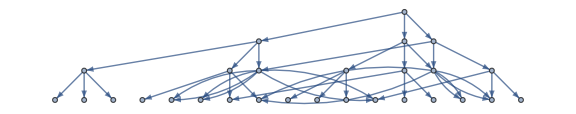

```mathematica
graph=showGraph@evo
```

## Todo

Increase efficiency

Construct full CA histories from each possible path

Find branching/merging factors for different layers

Compare different sets of rules

Compare different initial conditions